## Simplified FK of SRSPM

```mathematica
SetDirectory[NotebookDirectory[]]
(*<<ed5314utils_en.m*)
```

/home/nightmareforev/git/root_tracking/Mathematica/SRSPM

```mathematica
rotZ[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
```

```mathematica
(*fixed platform*)
b1 = {1, 0, 0};
b2 = rotZ[2*0.2985].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
tempa = Table[Symbol["b"<>ToString[i]],{i, 6}];
b = Table[rotZ[(2π/3-2*0.2985)/2].tempa[[i]],{i, Length[tempa]}];
ashift=b-{b[[1]],b[[1]],b[[1]],b[[1]],b[[1]],b[[1]]}
```

{{0.,0.,0.},{-0.509373,0.294087,0.},{-1.68835,-0.386598,0.},{-1.68835,-0.974772,0.},{-0.509373,-1.65546,0.},{-2.22045×10^-16,-1.36137,0.}}

```mathematica
(*moving platform*)
a1 = {0.5803, 0, 0};
a2 = rotZ[2*0.6573].a1;
a3 = rotZ[2π/3].a1;
a4 = rotZ[2π/3].a2;
a5 = rotZ[4π/3].a1;
a6 = rotZ[4π/3].a2;
tempa = Table[Symbol["a"<>ToString[i]],{i, 6}];
a = Table[rotZ[(2π/3-2*0.6573)/2].tempa[[i]],{i, Length[tempa]}];
ashift=a-{a[[1]],a[[1]],a[[1]],a[[1]],a[[1]],a[[1]]}
```

{{0.,0.,0.},{-0.614103,0.354553,0.},{-0.996139,0.133984,0.},{-0.996139,-0.575121,0.},{-0.614103,-0.795689,0.},{-1.11022×10^-16,-0.441137,0.}}

```mathematica
lvals = {1.4458208723874426,1.568679047566447,1.57865471573012,1.3393859531342835,1.152479064455009,1.286875291086054}
```

{1.44582,1.56868,1.57865,1.33939,1.15248,1.28688}

```mathematica
l = {l1, l2, l3, l4, l5, l6}
```

{l1,l2,l3,l4,l5,l6}

```mathematica
sub={b2x->-0.5093734006873172,b2y->0.2940868700048578,b2z->0,b3x->-1.6883547421176872,b3y->-0.3865983248395124,b3z->0,b4x->-1.6883547421176874,b4y->-0.9747720648492277,b4z->0,b5x->-0.5093734006873175,b5y->-1.6554572596935981,b5z->0,b6x->-2.220446049250313*10^-16,b6y->-1.3613703896887406,b6z->0,t2x->-0.6141031970306339,t2y->0.35455264611584647,t2z->0,t3x->-0.9961387846155708,t3y->0.13398429678366627,t3z->0,t4x->-0.996138784615571,t4y->-0.5751209954480264,t4z->0,t5x->-0.6141031970306341,t5y->-0.7956893447802065,t5z->0,t6x->-1.1102230246251565*10^-16,t6y->-0.44113669866436034,t6z->0}
len=Inner[Rule, l, lvals, List]
```

{b2x→-0.509373,b2y→0.294087,b2z→0,b3x→-1.68835,b3y→-0.386598,b3z→0,b4x→-1.68835,b4y→-0.974772,b4z→0,b5x→-0.509373,b5y→-1.65546,b5z→0,b6x→-2.22045×10^-16,b6y→-1.36137,b6z→0,t2x→-0.614103,t2y→0.354553,t2z→0,t3x→-0.996139,t3y→0.133984,t3z→0,t4x→-0.996139,t4y→-0.575121,t4z→0,t5x→-0.614103,t5y→-0.795689,t5z→0,t6x→-1.11022×10^-16,t6y→-0.441137,t6z→0}

{l1→1.44582,l2→1.56868,l3→1.57865,l4→1.33939,l5→1.15248,l6→1.28688}

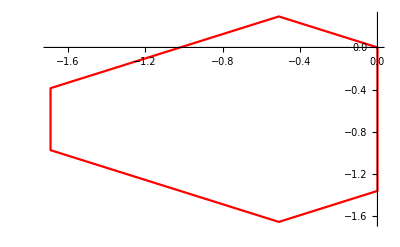

```mathematica
(*Fixed Platform*)
o1={0,0,0};
o2={b2x,b2y,b2z};
o3={b3x,b3y,b3z};
o4={b4x,b4y,b4z};
o5={b5x,b5y,b5z};
o6={b6x,b6y,b6z};
o={o1,o2,o3,o4,o5,o6,o1};
ListLinePlot[(o/.sub)[[;;, 1;;2]],PlotStyle->Red]
(*oj={bjx,bjy,bjz};*)
```

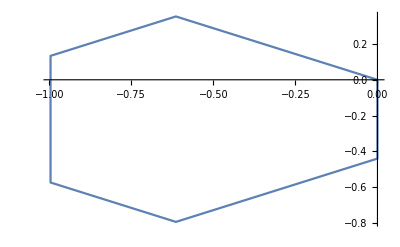

```mathematica
(*Moving platform*)
p1={0,0,0};
p2={t2x,t2y,t2z};
p3={t3x,t3y,t3z};
p4={t4x,t4y,t4z};
p5={t5x,t5y,t5z};
p6={t6x,t6y,t6z};
p={p1,p2,p3,p4,p5,p6,p1};
ListLinePlot[(p/.sub)[[;;, 1;;2]]]
(*pj={tjx,tjy,tjz};*)
```

```mathematica
Cmat={{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}
```

{{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}

```mathematica
Rmat=Simplify[(IdentityMatrix[3]+Cmat).Inverse[(IdentityMatrix[3]-Cmat)]];
```

```mathematica
xvec={x,y,z};
```

```mathematica
p1o=xvec+Rmat.p1;
p2o=xvec+Rmat.p2;
p3o=xvec+Rmat.p3;
p4o=xvec+Rmat.p4;
p5o=xvec+Rmat.p5;
p6o=xvec+Rmat.p6;
(*pjo=xvec+Rmat.pj;*)
```

```mathematica
eq1=(p1o-o1).(p1o-o1)-l1^2
```

-l1^2+x^2+y^2+z^2

```mathematica
(*monoprod[{a_,b_}]:=a.b;
eqj=FullSimplify[monoprod[FullSimplify[monopoly[Factor[(pjo-oj).(pjo-oj)-lj^2][[3]],{bjx,bjy,bjz,tjx,tjy,tjz,lj}]]/.{ (x^2+y^2+z^2)-> w,1+c1^2+c2^2+c3^2-> c0,-1-c1^2-c2^2-c3^2-> -c0}]];*)
```

```mathematica
eq2=FullSimplify[Factor[(p2o-o2).(p2o-o2)-l2^2][[3]]];
eq3=FullSimplify[Factor[(p3o-o3).(p3o-o3)-l3^2][[3]]];
eq4=FullSimplify[Factor[(p4o-o4).(p4o-o4)-l4^2][[3]]];
eq5=FullSimplify[Factor[(p5o-o5).(p5o-o5)-l5^2][[3]]];
eq6=FullSimplify[Factor[(p6o-o6).(p6o-o6)-l6^2][[3]]];
```

```mathematica
nsol=Timing[NSolve[N[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len),50]=={0,0,0,0,0,0},{x,y,z,c1,c2,c3},Method-> "HomotopyContinuation"]];
```

```mathematica
len
```

{l1→1.44582,l2→1.56868,l3→1.57865,l4→1.33939,l5→1.15248,l6→1.28688}

```mathematica
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@nsol[[2]](*Residue check*)
```

{1.14181×10^20,1.14181×10^20,7.40635×10^19,7.40635×10^19,3.60977×10^20,3.60977×10^20,1.08295×10^20,1.08295×10^20,1.14181×10^20,1.14181×10^20,7.40635×10^19,7.40635×10^19,3.60977×10^20,3.60977×10^20,1.08295×10^20,1.08295×10^20,1.47038×10^18,1.47038×10^18,2.70781×10^17,2.70781×10^17,1.19152×10^18,1.19152×10^18,2.26779×10^18,2.26779×10^18,9.04762×10^17,9.04762×10^17,4.42185×10^19,4.42185×10^19,5.60553×10^19,5.60553×10^19,4.54954×10^17,4.54954×10^17,1.09397×10^18,1.09397×10^18,1.02686×10^18,1.02686×10^18,9.51353×10^17,9.51353×10^17,6.76953×10^17,6.76953×10^17,9.04762×10^17,9.04762×10^17,4.42185×10^19,4.42185×10^19,5.60553×10^19,5.60553×10^19,4.54954×10^17,4.54954×10^17,2.70384×10^18,2.70384×10^18,8.34402×10^16,8.34402×10^16,3.11619×10^16,3.11619×10^16,2.33467×10^16,2.33467×10^16,1.09065×10^17,1.09065×10^17,5.72344×10^16,5.72344×10^16,6.38823×10^16,6.38823×10^16,3.92524×10^16,3.92524×10^16,5.80955×10^16,5.80955×10^16,3.61221×10^16,3.61221×10^16,2.49088×10^16,2.49088×10^16,1.57099×10^16,1.57099×10^16,2.76249×10^16,2.76249×10^16,2.49088×10^16,2.49088×10^16,2.76249×10^16,2.76249×10^16,3.61221×10^16,3.61221×10^16,1.57099×10^16,1.57099×10^16,2.36942×10^17,2.36942×10^17,1.74772×10^17,1.74772×10^17,3.92524×10^16,3.92524×10^16,5.72344×10^16,5.72344×10^16,5.80955×10^16,5.80955×10^16,6.38823×10^16,6.38823×10^16,1.74772×10^17,1.74772×10^17,6.94265×10^17,6.94265×10^17,2.14906×10^14,2.14906×10^14,5.4768×10^14,5.4768×10^14,2.06054×10^18,2.06054×10^18,9.94368×10^15,9.94368×10^15,2.21634×10^15,2.21634×10^15,3.80577×10^14,3.80577×10^14,8.61902×10^17,8.61902×10^17,1.07162×10^18,1.07162×10^18,1.07162×10^18,1.07162×10^18,5.22385×10^16,5.22385×10^16,5.22385×10^16,5.22385×10^16,8.07188×10^16,8.07188×10^16,1.64713×10^16,1.64713×10^16,1.64713×10^16,1.64713×10^16,3.45464×10^16,3.45464×10^16,985534.,985534.,893276.,893276.,893276.,893276.,339666.,339666.,220731.,220731.,220731.,220731.,36912.3,36912.3,81959.9,81959.9,81959.9,81959.9,1.6764×10^-15,1.6764×10^-15,1.36087×10^-15,1.36087×10^-15,1.33227×10^-15,2.18759×10^-15,4.15407×10^-15,2.05016×10^-15,3.25771×10^-15,3.25771×10^-15,2.18759×10^-15,4.15407×10^-15,1.33227×10^-15,2.05016×10^-15}

```mathematica
nsol[[2]][[3]]
```

{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→-6.62991×10^16+5.54034×10^16 ⅈ,c1→0.772379-0.517395 ⅈ,c2→0.554854+0.875733 ⅈ,c3→-0.0920629+0.937177 ⅈ}

```mathematica
Select[c3/.nsol[[2]],Abs[Im[#]]≤ 10^-6&](*Reals filter*)
```

{-1.21096,-1.21096,0.825788,0.825788,0.825788,0.825788,-1.21096,-1.21096,1.67247,1.67247,-0.597917,-0.597917,-0.597917,-0.597917,1.67247,1.67247,5.14031×10^16+3.58974×10^-60 ⅈ,5.14031×10^16-3.58974×10^-60 ⅈ,-3.22454,-3.22454,0.310122,0.310122,0.310122,0.310122,-3.22454,-3.22454,-1.46974×10^16+5.30039×10^-62 ⅈ,-1.46974×10^16-5.30039×10^-62 ⅈ,48.9051,48.9051,-0.0204478,-0.0204478,-0.0204478,-0.0204478,48.9051,48.9051,-6.67026×10^14-9.63601×10^-59 ⅈ,-6.67026×10^14+9.63601×10^-59 ⅈ,-2.41916×10^14-2.01824×10^-62 ⅈ,-2.41916×10^14+2.01824×10^-62 ⅈ,-7.75444×10^13-4.25359×10^-59 ⅈ,-7.75444×10^13+4.25359×10^-59 ⅈ,286092.,286092.,-221217.-1.41854×10^-74 ⅈ,-221217.+1.41854×10^-74 ⅈ,194308.-1.74305×10^-75 ⅈ,194308.+1.74305×10^-75 ⅈ,-1.35802×10^-6,-1.35802×10^-6,1.75631×10^-6,1.75631×10^-6,-1.99952×10^-6,-1.99952×10^-6,2.54113×10^-16,2.54113×10^-16,4.19615×10^-16,4.19615×10^-16,9.86341×10^-16,5.43361×10^-16,9.55591×10^-16,5.93303×10^-16,4.65813×10^-16,4.65813×10^-16,5.43361×10^-16,9.55591×10^-16,9.86341×10^-16,5.93303×10^-16}

```mathematica
(*Coefficient[Times@@(α{2,4,4,4,4,4}),α^6]
Coefficient[Times@@(α{2,3,3,3,3,3}),α^6]
Coefficient[Times@@(α{2,2,2,2,2,2}+β{0,2,2,2,2,2}),α^3 β^3]
Coefficient[Times@@(α{2,1,1,1,1,1}+β{0,2,2,2,2,2}),α^3 β^3]*)(*multi-homogenoeus Bezout number calculation for different grouping and formulation*)
```

## Use these solutions till I figure out how to get the others

```mathematica
reqsol=nsol[[2,-14;;]];
```

```mathematica
(* Residue check *)
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@reqsol
```

{1.6764×10^-15,1.6764×10^-15,1.36087×10^-15,1.36087×10^-15,1.33227×10^-15,2.18759×10^-15,4.15407×10^-15,2.05016×10^-15,3.25771×10^-15,3.25771×10^-15,2.18759×10^-15,4.15407×10^-15,1.33227×10^-15,2.05016×10^-15}

### These are solutions for the center of the moving platform

```mathematica
transformedsol=Table[Inner[Rule,{x,y,z,c1,c2,c3},(Join[(rotZ[(2π/3-2*0.2985)/2].{1,0,0}+{x,y,z}-Rmat.rotZ[(2π/3-2*0.6573)/2].{0.5803,0,0}),{c1,c2,c3}]/.reqsol[[ii]]),List],{ii,1,14}];
```

```mathematica
(* x y z c1 c2 c3 *)
```

```mathematica
transformedsol//MatrixForm
```

(x→1.87004+0. ⅈ | y→-0.523587+0. ⅈ | z→0.-0.926899 ⅈ | c1→0.-0.105691 ⅈ | c2→0.+0.715478 ⅈ | c3→2.54113×10^-16
x→1.87004+0. ⅈ | y→-0.523587+0. ⅈ | z→0.+0.926899 ⅈ | c1→0.+0.105691 ⅈ | c2→0.-0.715478 ⅈ | c3→2.54113×10^-16
x→-1.07203+0. ⅈ | y→1.69713+0. ⅈ | z→0.-0.968525 ⅈ | c1→0.-0.663889 ⅈ | c2→0.-0.342257 ⅈ | c3→4.19615×10^-16
x→-1.07203+0. ⅈ | y→1.69713+0. ⅈ | z→0.+0.968525 ⅈ | c1→0.+0.663889 ⅈ | c2→0.+0.342257 ⅈ | c3→4.19615×10^-16
x→0.218338 | y→-0.790621 | z→0.724086 | c1→-0.715499 | c2→-0.645258 | c3→9.86341×10^-16
x→0.2 | y→-2.77556×10^-16 | z→1.28 | c1→0.2 | c2→-6.00667×10^-17 | c3→5.43361×10^-16
x→-0.513695 | y→-0.519996 | z→-0.798723 | c1→-0.333759 | c2→-0.951699 | c3→9.55591×10^-16
x→0.524434 | y→0.268509 | z→1.0308 | c1→0.603749 | c2→-0.188561 | c3→5.93303×10^-16
x→-0.73374+0. ⅈ | y→-2.15448+0. ⅈ | z→0.-1.38947 ⅈ | c1→0.+0.633855 ⅈ | c2→0.-0.427583 ⅈ | c3→4.65813×10^-16
x→-0.73374+0. ⅈ | y→-2.15448+0. ⅈ | z→0.+1.38947 ⅈ | c1→0.-0.633855 ⅈ | c2→0.+0.427583 ⅈ | c3→4.65813×10^-16
x→0.2 | y→-2.77556×10^-16 | z→-1.28 | c1→-0.2 | c2→6.00667×10^-17 | c3→5.43361×10^-16
x→-0.513695 | y→-0.519996 | z→0.798723 | c1→0.333759 | c2→0.951699 | c3→9.55591×10^-16
x→0.218338 | y→-0.790621 | z→-0.724086 | c1→0.715499 | c2→0.645258 | c3→9.86341×10^-16
x→0.524434 | y→0.268509 | z→-1.0308 | c1→-0.603749 | c2→0.188561 | c3→5.93303×10^-16)

```mathematica
Chop[transformedsol]//MatrixForm
```

(x→1.87004 | y→-0.523587 | z→0.-0.926899 ⅈ | c1→0.-0.105691 ⅈ | c2→0.+0.715478 ⅈ | c3→0
x→1.87004 | y→-0.523587 | z→0.+0.926899 ⅈ | c1→0.+0.105691 ⅈ | c2→0.-0.715478 ⅈ | c3→0
x→-1.07203 | y→1.69713 | z→0.-0.968525 ⅈ | c1→0.-0.663889 ⅈ | c2→0.-0.342257 ⅈ | c3→0
x→-1.07203 | y→1.69713 | z→0.+0.968525 ⅈ | c1→0.+0.663889 ⅈ | c2→0.+0.342257 ⅈ | c3→0
x→0.218338 | y→-0.790621 | z→0.724086 | c1→-0.715499 | c2→-0.645258 | c3→0
x→0.2 | y→0 | z→1.28 | c1→0.2 | c2→0 | c3→0
x→-0.513695 | y→-0.519996 | z→-0.798723 | c1→-0.333759 | c2→-0.951699 | c3→0
x→0.524434 | y→0.268509 | z→1.0308 | c1→0.603749 | c2→-0.188561 | c3→0
x→-0.73374 | y→-2.15448 | z→0.-1.38947 ⅈ | c1→0.+0.633855 ⅈ | c2→0.-0.427583 ⅈ | c3→0
x→-0.73374 | y→-2.15448 | z→0.+1.38947 ⅈ | c1→0.-0.633855 ⅈ | c2→0.+0.427583 ⅈ | c3→0
x→0.2 | y→0 | z→-1.28 | c1→-0.2 | c2→0 | c3→0
x→-0.513695 | y→-0.519996 | z→0.798723 | c1→0.333759 | c2→0.951699 | c3→0
x→0.218338 | y→-0.790621 | z→-0.724086 | c1→0.715499 | c2→0.645258 | c3→0
x→0.524434 | y→0.268509 | z→-1.0308 | c1→-0.603749 | c2→0.188561 | c3→0)

```mathematica
roots = transformedsol
```

{{x→1.87004+0. ⅈ,y→-0.523587+0. ⅈ,z→0.-0.926899 ⅈ,c1→0.-0.105691 ⅈ,c2→0.+0.715478 ⅈ,c3→2.54113×10^-16},{x→1.87004+0. ⅈ,y→-0.523587+0. ⅈ,z→0.+0.926899 ⅈ,c1→0.+0.105691 ⅈ,c2→0.-0.715478 ⅈ,c3→2.54113×10^-16},{x→-1.07203+0. ⅈ,y→1.69713+0. ⅈ,z→0.-0.968525 ⅈ,c1→0.-0.663889 ⅈ,c2→0.-0.342257 ⅈ,c3→4.19615×10^-16},{x→-1.07203+0. ⅈ,y→1.69713+0. ⅈ,z→0.+0.968525 ⅈ,c1→0.+0.663889 ⅈ,c2→0.+0.342257 ⅈ,c3→4.19615×10^-16},{x→0.218338,y→-0.790621,z→0.724086,c1→-0.715499,c2→-0.645258,c3→9.86341×10^-16},{x→0.2,y→-2.77556×10^-16,z→1.28,c1→0.2,c2→-6.00667×10^-17,c3→5.43361×10^-16},{x→-0.513695,y→-0.519996,z→-0.798723,c1→-0.333759,c2→-0.951699,c3→9.55591×10^-16},{x→0.524434,y→0.268509,z→1.0308,c1→0.603749,c2→-0.188561,c3→5.93303×10^-16},{x→-0.73374+0. ⅈ,y→-2.15448+0. ⅈ,z→0.-1.38947 ⅈ,c1→0.+0.633855 ⅈ,c2→0.-0.427583 ⅈ,c3→4.65813×10^-16},{x→-0.73374+0. ⅈ,y→-2.15448+0. ⅈ,z→0.+1.38947 ⅈ,c1→0.-0.633855 ⅈ,c2→0.+0.427583 ⅈ,c3→4.65813×10^-16},{x→0.2,y→-2.77556×10^-16,z→-1.28,c1→-0.2,c2→6.00667×10^-17,c3→5.43361×10^-16},{x→-0.513695,y→-0.519996,z→0.798723,c1→0.333759,c2→0.951699,c3→9.55591×10^-16},{x→0.218338,y→-0.790621,z→-0.724086,c1→0.715499,c2→0.645258,c3→9.86341×10^-16},{x→0.524434,y→0.268509,z→-1.0308,c1→-0.603749,c2→0.188561,c3→5.93303×10^-16}}

```mathematica
Join[roots[[5;; 8]], roots[[11;;]]]//Chop//MatrixForm
```

(x→0.218338 | y→-0.790621 | z→0.724086 | c1→-0.715499 | c2→-0.645258 | c3→0
x→0.2 | y→0 | z→1.28 | c1→0.2 | c2→0 | c3→0
x→-0.513695 | y→-0.519996 | z→-0.798723 | c1→-0.333759 | c2→-0.951699 | c3→0
x→0.524434 | y→0.268509 | z→1.0308 | c1→0.603749 | c2→-0.188561 | c3→0
x→0.2 | y→0 | z→-1.28 | c1→-0.2 | c2→0 | c3→0
x→-0.513695 | y→-0.519996 | z→0.798723 | c1→0.333759 | c2→0.951699 | c3→0
x→0.218338 | y→-0.790621 | z→-0.724086 | c1→0.715499 | c2→0.645258 | c3→0
x→0.524434 | y→0.268509 | z→-1.0308 | c1→-0.603749 | c2→0.188561 | c3→0)